```mathematica
ClearAll[m0];ClearAll[Γ0];ClearAll[S];ClearAll[L0];ClearAll[decays];

(** Nucleons **)
m0[p[938]]=0.938;Γ0[p[938]]=0.;S[p[938]]=1/2;L0[p[938]]=0;

m0[p[1440]]=1.440;Γ0[p[1440]]=0.200;S[p[1440]]=1/2;L0[p[1440]]=0;
decays[p[1440]]={
{{p[938],pi},0.70},
{{p[938],pipi},0.05},
{{Δ[1232],pi},0.25}
};

m0[p[1520]]=1.520;Γ0[p[1520]]=0.125;S[p[1520]]=3/2;L0[p[1520]]=1;
decays[p[1520]]={
{{p[938],pi},0.60},
{{p[938],pipi},0.15},
{{Δ[1232],pi},0.25}
};

m0[p[1535]]=1.535;Γ0[p[1535]]=0.150;S[p[1535]]=1/2;L0[p[1535]]=1;
decays[p[1535]]={
{{p[938],gamma},0.001},
{{p[938],pi},0.549},
{{p[938],eta},0.35},
{{p[938],pipi},0.05},
{{p[1440],pi},0.05}
};

m0[p[1650]]=1.650;Γ0[p[1650]]=0.150;S[p[1650]]=1/2;L0[p[1650]]=1;
decays[p[1650]]={
{{p[938],pi},0.65},
{{p[938],eta},0.05},
{{p[938],pipi},0.05},
{{Δ[1232],pi},0.10},
{{p[1440],pi},0.05},
{{Lambda,Ka},0.10}
};

m0[p[1675]]=1.675;Γ0[p[1675]]=0.140;S[p[1675]]=5/2;L0[p[1675]]=1;
decays[p[1675]]={
{{p[938],pi},0.45},
{{Δ[1232],pi},0.55}
};

m0[p[1680]]=1.680;Γ0[p[1680]]=0.120;S[p[1680]]=5/2;L0[p[1680]]=2;
decays[p[1680]]={
{{p[938],pi},0.65},
{{p[938],pipi},0.20},
{{Δ[1232],pi},0.15}
};

m0[p[1700]]=1.700;Γ0[p[1700]]=0.100;S[p[1700]]=3/2;L0[p[1700]]=1;
decays[p[1700]]={
{{p[938],pi},0.10},
{{p[938],eta},0.05},
{{p[938],rho},0.05},
{{p[938],pipi},0.45},
{{Δ[1232],pi},0.35}
};

m0[p[1710]]=1.710;Γ0[p[1710]]=0.110;S[p[1710]]=1/2;L0[p[1710]]=0;
decays[p[1710]]={
{{p[938],pi},0.15},
{{p[938],eta},0.20},
{{p[938],rho},0.05},
{{p[938],pipi},0.20},
{{Δ[1232],pi},0.20},
{{p[1440],pi},0.10},
{{Lambda,Ka},0.10}
};

m0[p[1720]]=1.720;Γ0[p[1720]]=0.150;S[p[1720]]=3/2;L0[p[1720]]=2;
decays[p[1720]]={
{{p[938],pi},0.15},
{{p[938],rho},0.25},
{{p[938],pipi},0.45},
{{Δ[1232],pi},0.10},
{{Lambda,Ka},0.05}
};

(*1900*)

(*1990*)

(*2080*)

m0[p[2190]]=2.190;Γ0[p[2190]]=0.550;S[p[2190]]=7/2;L0[p[2190]]=3;
decays[p[2190]]={
{{p[938],pi},0.35},
{{p[938],rho},0.30},
{{p[938],pipi},0.15},
{{Δ[1232],pi},0.15},
{{p[1440],pi},0.05}
};

m0[p[2220]]=2.220;Γ0[p[2220]]=0.550;S[p[2220]]=9/2;L0[p[2220]]=4;
decays[p[2220]]={
{{p[938],pi},0.35},
{{p[938],rho},0.25},
{{p[938],pipi},0.20},
{{Δ[1232],pi},0.20}
};

m0[p[2250]]=2.250;Γ0[p[2250]]=0.470;S[p[2250]]=9/2;L0[p[2250]]=3;
decays[p[2250]]={
{{p[938],pi},0.30},
{{p[938],rho},0.25},
{{p[938],pipi},0.20},
{{Δ[1232],pi},0.20},
{{p[1440],pi},0.05}
};

ps={p[1440],p[1520],p[1535],p[1650],p[1675],p[1680],p[1700],p[1710],p[1720],p[2190],p[2220],p[2250]};



(** Delta particles **)
m0[Δ[1232]]=1.232;Γ0[Δ[1232]]=0.115;S[Δ[1232]]=3/2;L0[Δ[1232]]=0;
decays[Δ[1232]]={
{{p[938],gamma}, 0.01},
{{p[938],pi},0.99}
};

m0[Δ[1600]]=1.700;Γ0[Δ[1600]]=0.200;S[Δ[1600]]=3/2;L0[Δ[1600]]=0;
decays[Δ[1600]]={
{{p[938],pi},0.15},
{{Δ[1232],pi},0.55},
{{p[1440],pi},0.30}
};

m0[Δ[1620]]=1.675;Γ0[Δ[1620]]=0.180;S[Δ[1620]]=1/2;L0[Δ[1620]]=0;
decays[Δ[1620]]={
{{p[938],pi},0.25},
{{Δ[1232],pi},0.60},
{{p[1440],pi},0.15}
};

m0[Δ[1700]]=1.750;Γ0[Δ[1700]]=0.300;S[Δ[1700]]=3/2;L0[Δ[1700]]=1;
decays[Δ[1700]]={
{{p[938],pi},0.20},
{{p[938],rho},0.10},
{{Δ[1232],pi},0.55},
{{p[1440],pi},0.15}
};

(*(*1900*)m0[Δ[4]]=1.850;Γ0[Δ[4]]=0.240;S[Δ[4]]=1/2;*)

m0[Δ[1905]]=1.880;Γ0[Δ[1905]]=0.280;S[Δ[1905]]=5/2;L0[Δ[1905]]=2;
decays[Δ[1905]]={
{{p[938],pi},0.20},
{{p[938],rho},0.60},
{{Δ[1232],pi},0.10},
{{p[1440],pi},0.10}
};

m0[Δ[1910]]=1.900;Γ0[Δ[1910]]=0.250;S[Δ[1910]]=1/2;L0[Δ[1910]]=2;
decays[Δ[1910]]={
{{p[938],pi},0.35},
{{p[938],rho},0.40},
{{Δ[1232],pi},0.15},
{{p[1440],pi},0.10}
};

m0[Δ[1920]]=1.920;Γ0[Δ[1920]]=0.150;S[Δ[1920]]=3/2;L0[Δ[1920]]=2;
decays[Δ[1920]]={
{{p[938],pi},0.15},
{{p[938],rho},0.30},
{{Δ[1232],pi},0.30},
{{p[1440],pi},0.25}
};

(*(*1930*)m0[Δ[8]]=1.930;Γ0[Δ[8]]=0.250;S[Δ[8]]=5/2;*)

m0[Δ[1950]]=1.950;Γ0[Δ[1950]]=0.250;S[Δ[1950]]=7/2;L0[Δ[1950]]=2;
decays[Δ[1950]]={
{{p[938],gamma},0.01},
{{p[938],pi},0.44},
{{p[938],rho},0.15},
{{Δ[1232],pi},0.20},
{{p[1440],pi},0.20}
};

Δs={Δ[1600],Δ[1620],Δ[1700], Δ[1905],Δ[1910],Δ[1920],Δ[1950]};


(*Decay products*)
m0[pi]=0.137;Γ0[pi]=0.;S[pi]=1/2;
m0[gamma]=0.;Γ0[gamma]=0.;S[gamma]=1;
m0[pipi]=2m0[pi];Γ0[pipi]=0.;S[pipi]=1;
m0[eta]=0.548;Γ0[eta]=0.;S[eta]=1;
m0[rho]=0.775;Γ0[rho]=0.149;S[rho]=1;
m0[Lambda]=1.116;Γ0[Lambda]=0.;S[Lambda]=1/2;
m0[Ka]=0.498;Γ0[Ka]=0.;S[Ka]=0;
mBound=m0[p[938]]+m0[pi];
m0[p_]:=Throw["No nominal mass found for "<>ToString[p]];
Γ0[p_]:=Throw["No nominal width found for "<>ToString[p]];
S[p_]:=Throw["No spin found for "<>ToString[p]];
L0[p_]:=Throw["No orbital angular momentum found for "<>ToString[p]];


(* Define the width function Γ *)
BR[particle_,outs_]:=Select[decays[particle],#[[1]]==outs&,1][[1,2]];
Γ0[hIn_,hOuts_]:=Γ0[hIn] BR[hIn,hOuts];

pCMS[eCM_,mA_,mB_]:=If[eCM≤mA+mB,0.,1/(2.eCM)*Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]];
p[mDistribution_][eCM_,hA_,hB_]:=Module[{m0A,m0B},m0A=m0[hA];m0B=m0[hB];
If[Γ0[hA]==Γ0[hB]==0.,
If[eCM<m0A+m0B,Return[0],Return@pCMS[eCM,m0A,m0B]]
];
If[Γ0[hA]==0.,
If[eCM<m0A,Return[0],
Return@NIntegrate[pCMS[eCM,m0A,mB]mDistribution[hB,mB],{mB,0.,eCM-m0A}]
]];
If[Γ0[hB]==0.,
If[eCM<m0B,Return[0],
Return@NIntegrate[pCMS[eCM,mA,m0B]mDistribution[hA,mA],{mA,0.,eCM-m0B}]
]];
NIntegrate[pCMS[eCM,mA,mB]mDistribution[hA,mA]mDistribution[hB,mB],{mA,0.,eCM},{mB,0.,eCM-mA}]];

ClearAll[a0];
breitWigner[Γ0_Real,m0_Real,m_Real]:=Γ0/((m0-m)^2+Γ0^2/4)
a0[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a0: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ0[particle],m0[particle],m]/(2Pi)
];
p0Mean=p[a0];

ClearAll[Γ];
Γ[hIn_,hOuts_,m_Real]:= Module[{p0,p0res},
p0=p0Mean[m,hOuts[[1]],hOuts[[2]]];
p0res= p0Mean[m0[hIn],hOuts[[1]],hOuts[[2]]];
If[p0res==0,Throw["Mean p at resonance is zero for "<>ToString[hIn]<>"-->"<>ToString[hOuts]]];
If[p0==0,Return[0]];
Γ0[hIn,hOuts] * m0[hIn]/m * (p0/p0res)^(2L0[hIn]+1) * 1.2/(1. + 0.2(p0/p0res)^(2L0[hIn]))
];
Γ[h_,m_]:=Sum[Γ[h,decs[[1]],m],{decs,decays[h]}];


(* Define the mass distribution function and <p> *)
ClearAll[aN]; ClearAll[a];
aN[particle_]:=aN[particle]=Re@NIntegrate[Γ[particle,m]/((m0[particle]-m)^2+Γ[particle,m]^2/4),{m,mBound,Infinity}];

a[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ[particle,m],m0[particle],m]/aN[particle]
];
pMean=p[a];


(* Matrix elements and cross-sections *)
matrixElement[eCM_,{p[938],Δ[1232]},mA_,mB_]:=40000 * (m0[Δ[1232]] Γ0[Δ[1232]])^2/((eCM^2 -m0[Δ[1232]]^2)^2 +( m0[Δ[1232]] Γ0[Δ[1232]])^2);
matrixElement[eCM_,{Δ[1232],Δ[1232]},mA_,mB_]:=2.8;
matrixElement[eCM_,{p[938],p[ex_]},mA_,mB_]:=6.3/((mB-mA)^2(mB+mA)^2);
matrixElement[eCM_,{p[938],Δ[ex_]},mA_,mB_]:=12/((mB-mA)^2(mB+mA)^2);
matrixElement[eCM_,{Δ[938],p[ex_]},mA_,mB_]:=3.5/((mB-mA)^2(mB+mA)^2);
matrixElement[eCM_,{Δ[938],Δ[ex_]},mA_,mB_]:=3.5/((mB-mA)^2(mB+mA)^2);

sigmapp[eCM_,{hA_,hB_}]:=If[eCM≤2m0[p[938]],0,
(2S[hA]+1)(2S[hB]+1) * pMean[eCM,hA,hB]/pMean[eCM,p[938],p[938]] * matrixElement[eCM,{hA,hB},m0[hA],m0[hB]]/eCM^2
];
```

```mathematica
(* Summed cross-sections *)
sigmaNNstar[eCM_]:=Sum[sigmapp[eCM,{p[938],pstar}],{pstar,ps}];
```

```mathematica
sigmaNNstar[3.]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {1.07527}. NIntegrate obtained 0.756828 and 1.51334×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {1.61493}. NIntegrate obtained 0.595564 and 7.36569×10^-7 for the integral and error estimates.

6.97705

```mathematica
p0Mean[m0[p[1700]],p[938],rho]
```

0.106846

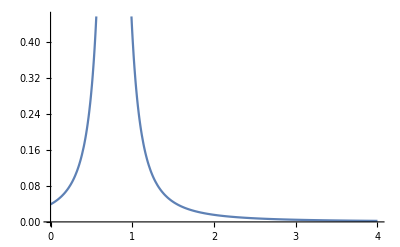

```mathematica
Plot[a0[rho,m],{m,0,4.}]
```

```mathematica
m0[p[1700]]
```

1.7

```mathematica
m0[p[938]]
```

0.938

```mathematica
{mB,mBound,m0[p[1700]]-m0[p[938]]}
```

{mB,1.075,0.762}

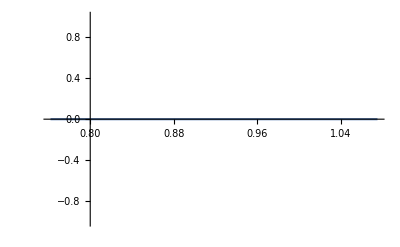

```mathematica
Plot[pCMS[m0[p[1700]],m0[p[938]],mB],{mB,mBound,m0[p[1700]]-m0[p[938]]}]
```

```mathematica
ptsNΔ=Monitor[Table[{eCM,sigmapp[eCM,{p[938],Δ[1232]}]},{eCM,2.,8.,0.05}],
{ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

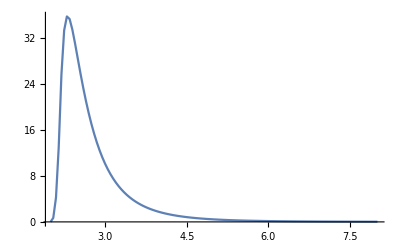

```mathematica
ListLinePlot[ptsNΔ,PlotRange->All]
```